```mathematica
poly4[x_, A_, B_, C1_, D1_]:=A*x^3+ B*x^2 +C1*x +D1
poly5[x_, preA_, A_, B_, C1_, D1_]:=preA*x^4+A*x^3+ B*x^2  +C1*x +D1
Dpoly5[x_, preA_, A_, B_, C1_, D1_]:=D[poly5[xp, preA, A, B, C1, D1], xp]//.{xp->x}
```

```mathematica
Manipulate[Plot[poly5[x, preA, 0, B, C1, 0], {x, -1, 1}], {preA, -10, 10},{A, -10, 10},{B, -10, 10},{C1, -10, 10}]
```

```mathematica
freepoly[x_, C1_, C2_, C3_]:= C1*x^4+ C2*x^2 +C3*x
freetan[x_, C1_, C2_, C3_, xt_]:=(D[freepoly[xtp, C1, C2, C3], xtp]//.{xtp->xt})*(x-xt)+freepoly[xt, C1, C2, C3]
dfree[x_, C1_, C2_, C3_]:=(D[freepoly[xtp, C1, C2, C3], xtp]//.{xtp->x})
```

```mathematica
Manipulate[Plot[{freepoly[x, C1, C2, C3], freetan[x, C1, C2, C3, xt]}, {x, -1, 1}, PlotRange->{-3, 2.5}], {{C1, 5}, -10, 10}, {{C2, -5}, -10, 10},{{C3, 2}, -10, 10}, {{xt, -0.708}, -1, 1}]
```

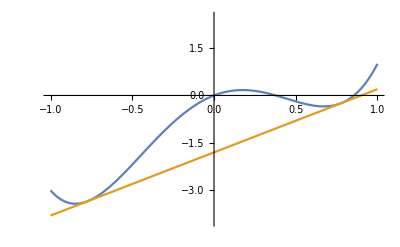

```mathematica
C1=5;
C2=-6;
C3=2;
xt=-0.708;
 xt = Sqrt[-C2/10];
Plot[{freepoly[x, C1, C2, C3], freetan[x, C1, C2, C3, xt]},{x, -1, 1}, PlotRange->{-4, 2.5}]
```

1/(√5)

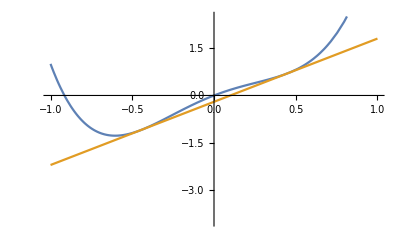

```mathematica
C1=5;
C2=-2;
C3=2;
xt=-0.5358;
xt = Sqrt[-C2/10]
Plot[{freepoly[x, C1, C2, C3], freetan[x, C1, C2, C3, xt]},{x, -1, 1}, PlotRange->{-4, 2.5}]
```

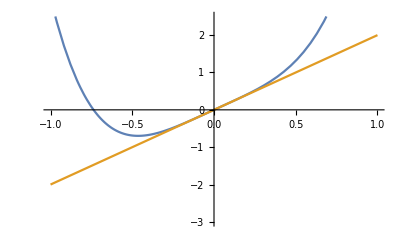

```mathematica
C1=5;
C2=0;
C3=2;
xt=0;
Plot[{freepoly[x, C1, C2, C3], freetan[x, C1, C2, C3, xt]},{x, -1, 1}, PlotRange->{-3, 2.5}]
```

```mathematica
Solve[{freepoly[x2, C1t, C2t, C3t]==freetan[x2, C1t, C2t, C3t, x1],
dfree[x1, C1t, C2t, C3t] == dfree[x2, C1t, C2t, C3t]}, {x1, x2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x2→x1},{x1→-(ⅈ √C2t)/(√2 √C1t),x2→(ⅈ √C2t)/(√2 √C1t)},{x1→(ⅈ √C2t)/(√2 √C1t),x2→-(ⅈ √C2t)/(√2 √C1t)},{x1→-(ⅈ √C2t)/(√6 √C1t),x2→-(ⅈ √C2t)/(√6 √C1t)},{x1→(ⅈ √C2t)/(√6 √C1t),x2→(ⅈ √C2t)/(√6 √C1t)}}

```mathematica
Solve[{freepoly[x2, 5, C2t, 2]==freetan[x2, 5, C2t, 2, x1],
dfree[x1, 5, C2t, 2] == dfree[x2, 5, C2t, 2]}, {x1, x2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x2→x1},{x1→-(ⅈ √C2t)/(√10),x2→(ⅈ √C2t)/(√10)},{x1→(ⅈ √C2t)/(√10),x2→-(ⅈ √C2t)/(√10)},{x1→-(ⅈ √C2t)/(√30),x2→-(ⅈ √C2t)/(√30)},{x1→(ⅈ √C2t)/(√30),x2→(ⅈ √C2t)/(√30)}}

```mathematica
Solve[D[freepoly[x2, C1t, C2t, C3t], {x2, 2}] == 0, x2]
```

{{x2→-(ⅈ √C2t)/(√6 √C1t)},{x2→(ⅈ √C2t)/(√6 √C1t)}}

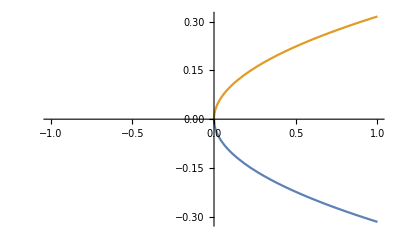

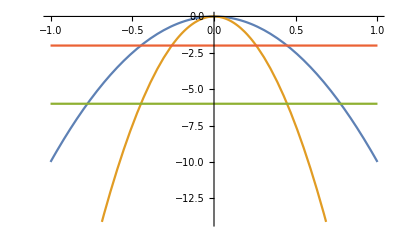

```mathematica
Plot[{-Sqrt[C2x/10], Sqrt[C2x/10]}, {C2x, -1, 1}]
Plot[{-10*x*x,-x*x*6*C1,-6,-2 }, {x, -1, 1}]
```